```mathematica
Clear["p","m","x","g","gg","λ","Δt","length","rnd","θ"]
$Assumptions=x>0&&x∈Reals&&λ>0&&λ∈Reals&&ν>0&&ν∈Reals;
```

```mathematica
𝒟=ChiSquareDistribution[ν];
p=PDF[𝒟,x]
m=Mean[𝒟]
K2=FullSimplify[-2 λ/p Integrate[(x-m)p,{x,0,x}]](*g^2[x]*)
g[x_]=Sqrt[K2]
gg[x_]=FullSimplify[Sqrt[K2] D[Sqrt[K2],x]]
```

Piecewise[{{(2^(-ν/2) ⅇ^(-x/2) x^(-1+ν/2))/Gamma[ν/2], x>0}, {0, True}}]

ν

4 x λ

2 √(x λ)

2 λ

```mathematica
ν=3;
λ=50;
Δt=1/10000;
length = 5 10^6;
SeedRandom[1]
rnd=RandomVariate[NormalDistribution[],length];
ξ[n_Integer]:=rnd[[n]]
vals=RecurrenceTable[{y[n+1]==1/(1+λ Δt)(y[n]+ λ m Δt+g[y[n]] √Δt ξ[n]+1/2 gg[y[n]]Δt(ξ[n]^2-1)),y[1]==1},y,{n,1,length}];
{FirstPosition[vals,_Complex],FirstCase[vals,_Complex]}
{Mean[vals],StandardDeviation[vals],Min[vals],Max[vals]}
```

{Missing[NotFound],Missing[NotFound]}

{2.97451,2.41476,0.00995026,26.7415}

-Graphics-

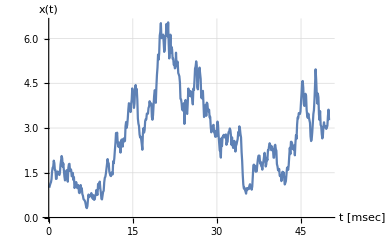

```mathematica
normFactor = CovarianceFunction[vals,0];
autocorrelationPlot=ListLinePlot[
{ParallelTable[{z Δt 10^3,CovarianceFunction[vals,z]/normFactor},{z,0,500,25}],
Table[{z Δt 10^3,Exp[-z Δt λ ]},{z,0,500,25}]},PlotRange->Full,GridLines->Automatic,
PlotLegends->Placed[{"Simulation","Exp[-λτ]"},{.8,.8}],AxesLabel->{"τ [msec]","C_xx(τ)"},LabelStyle -> Directive[Black,13,FontFamily->"Times New Roman"],
TicksStyle->Directive[Black, 13,FontFamily-> "Times New Roman"],PlotMarkers->{{Graphics[{Disk[]}],.04},""}]
timePlot=ListLinePlot[Thread[{Table[Δt x,{x,1,500}] 10^3,vals[[1;;500]]}],LabelStyle -> Directive[Black,13,FontFamily-> "Times New Roman"],
TicksStyle->Directive[Black, 13,FontFamily-> "Times New Roman"],
AxesLabel->{"t [msec]","x(t)"},GridLines->Automatic
]
```

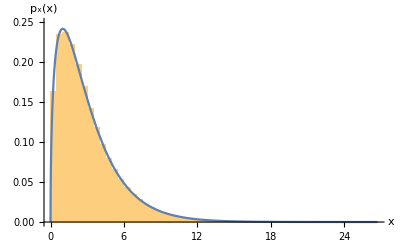

```mathematica
spoint = Solve[PDF[𝒟,x]==5 10^-3][[All,1,2]][[2]]//N;
h1= Histogram[vals,75,"PDF",ChartLegends->Placed[SwatchLegend[{"Hist"}],Scaled[{.5,1}]],PerformanceGoal->"Speed",PlotRange->{{0,Max[vals]},{0,.25}},AxesLabel-> {"x","p_x(x)"}];
h3= Histogram[vals,75,"PDF",PlotRange->{{spoint,Max[vals]},{0,5 10^-3}},PerformanceGoal->"Speed",AxesOrigin->{25,0},Ticks->{Automatic,Table[{i,ScientificForm[N@i,3]},{i,0,5 10^-3,5 10^-3/2}]}];
h2=Plot[PDF[𝒟,x],{x,0,Max[vals]},PlotLegends->Placed[LineLegend[{"PDF"}],Scaled[{.5,1}]]];
h4=Plot[PDF[𝒟,x],{x,spoint,Max[vals]},PlotRange->{{spoint,Max[vals]},{0,5 10^-3}}];
pdfPlot=Show[h1,h2,LabelStyle -> Directive[Black,13,FontFamily-> "Times New Roman"],AxesLabel-> {"x","p_x(x)"},
TicksStyle->Directive[Black, 13,FontFamily-> "Times New Roman"],Epilog-> Inset[Show[h3,h4],Scaled[{.8,.5}],Automatic,Automatic]]
```

200

{AndersonDarling,CramerVonMises,KolmogorovSmirnov,Kuiper,PearsonChiSquare,WatsonUSquare}

{The null hypothesis that the data is distributed according to the ChiSquareDistribution[3] is not rejected at the 0.1 percent level based on the Anderson-Darling test.,The null hypothesis that the data is distributed according to the ChiSquareDistribution[3] is not rejected at the 0.1 percent level based on the Cramér-von Mises test.,The null hypothesis that the data is distributed according to the ChiSquareDistribution[3] is not rejected at the 0.1 percent level based on the Kolmogorov-Smirnov test.,The null hypothesis that the data is distributed according to the ChiSquareDistribution[3] is not rejected at the 0.1 percent level based on the Kuiper test.,The null hypothesis that the data is distributed according to the ChiSquareDistribution[3] is not rejected at the 0.1 percent level based on the Pearson χ^2 test.,The null hypothesis that the data is distributed according to the ChiSquareDistribution[3] is not rejected at the 0.1 percent level based on the Watson U^2 test.}

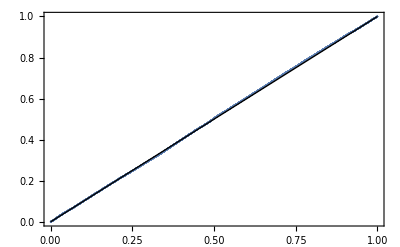

```mathematica
step = Round[1/(λ Δt)]
tests = DistributionFitTest[vals[[1;;;;step]],𝒟,"AllTests"]
Table[ToExpression[x<> "Test"] [vals[[1;;;;step]],𝒟,"TestConclusion",SignificanceLevel->0.001],{x,tests}]
ProbabilityPlot[vals[[1;;;;step]],𝒟]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["autocorrelationPlotChi.pdf",autocorrelationPlot]; Export["autocorrelationPlotChi.png",autocorrelationPlot];
Export["timePlotChi.pdf",timePlot]; Export["timePlotChi.png",timePlot];
Export["pdfPlotChi.pdf",pdfPlot];Export["pdfPlotChi.png",pdfPlot];
```